```mathematica
Q2ind[x_]:=1/x;
Q2Eq2[Qvol_,CVx_,x_]:=(1-Qvol^2)/x+Qvol^2*(CVx^2+1);
Q2Eq4[x_,CVx_,v_,CVv_]:=1/x+((1+CVx^2)*(1+CVv^2))/v;
Q2Eq5[x_,s_,q_]:=(1+s)/x+(s*(q-1))/x^2;
```

```mathematica
tickspecification2:=Table[{10^i,Superscript[10,i]},{i,-3,-1}];
```

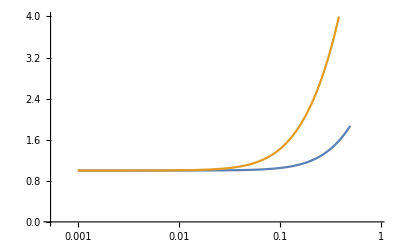

```mathematica
LogLinearPlot[{Sqrt[Q2Eq2[Qvol,1/(√10),10]/Q2ind[10]],Sqrt[Q2Eq2[Qvol,1/(√100),100]/Q2ind[100]]},{Qvol,10^-3,5*10^-1},PlotRange->{0,4}]
```

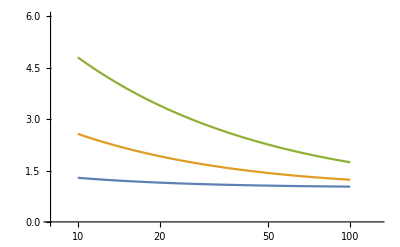

```mathematica
LogLinearPlot[{Sqrt[Q2Eq4[5,1/(√5),v,1/(√v)]/Q2ind[5]],Sqrt[Q2Eq4[50,1/(√50),v,1/(√v)]/Q2ind[50]],Sqrt[Q2Eq4[200,1/(√200),v,1/(√v)]/Q2ind[200]]},{v,10,10^2},PlotRange->{0,6}]
```

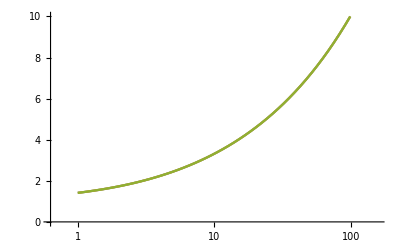

```mathematica
LogLinearPlot[{Sqrt[Q2Eq5[5,s,1]/Q2ind[5]],Sqrt[Q2Eq5[50,s,1]/Q2ind[50]],Sqrt[Q2Eq5[200,s,1]/Q2ind[200]]},{s,10^0,10^2},PlotRange->{0,10}]
```

```mathematica
Q2Eq6[x_,K_,CVx_]:=1/x*(1-K*x*(CVx^2+1));
Q2Eq6a[K_,Kx_,CVx_]:=K/Kx*(1-Kx*(CVx^2+1));
P[x_,v_]:=1;
Q2Eq7[x_,v_,Q2v_]:=1/x*(1-1/x*∑_(v=0)^∞ ((1/v-Q2v)*∑_(x=0)^v (x^2*P[x,v])+(v-v^2*Q2v)*∑_(x=v+1)^∞ P[x,v]));
Q2Eq8[x_,p_,k_]:=(1-(2*p-1)*k)/x;
```

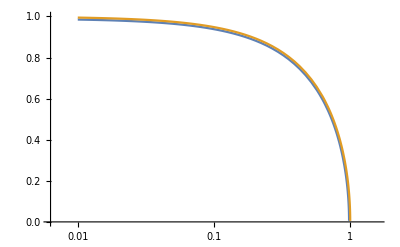

```mathematica
LogLinearPlot[{Sqrt[Q2Eq6a[0.02,Kx,1/(√(Kx/0.02))]/Q2ind[Kx/0.02]],Sqrt[Q2Eq6a[0.001,Kx,1/(√(Kx/0.001))]/Q2ind[Kx/0.001]]},{Kx,10^-2,1},PlotRange->{0,1}]
```

```mathematica
LogLinearPlot[{Sqrt[Q2Eq7[x,100,0]/Q2ind[x]],Sqrt[Q2Eq7[x,100,0]/Q2ind[x]]},{x,10^1,10^3},PlotRange->{0,1}]
```

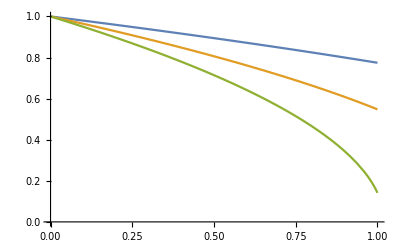

```mathematica
Plot[{Sqrt[Q2Eq8[10,0.7,k]/Q2ind[10]],Sqrt[Q2Eq8[10,0.85,k]/Q2ind[10]],Sqrt[Q2Eq8[10,0.99,k]/Q2ind[10]]},{k,0,1},PlotRange->{0,1}]
```